```mathematica
Exit[]
```

```mathematica
$Assumptions=x ∈ Reals
```

x∈Reals

Alternative utility-function

```mathematica
f[k_,x_]:=k x-Sqrt[1+k^2 x^2]
ra[f_]:= -Simplify[D[f[k,x],{x,2}]/D[f[k,x],x]]
```

```mathematica
Simplify[Expand[x ra[f]]]
```

k x ((k x)/(1+k^2 x^2)+1/(√(1+k^2 x^2)))

```mathematica
k=.;ra[f]/.x->0
```

k

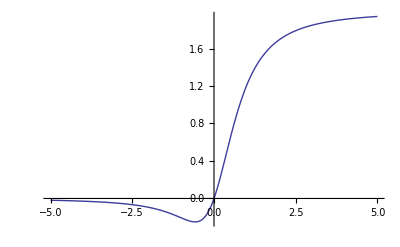

```mathematica
raf= ra[f];k=1;Plot[{x raf},{x,-5,5}]
```

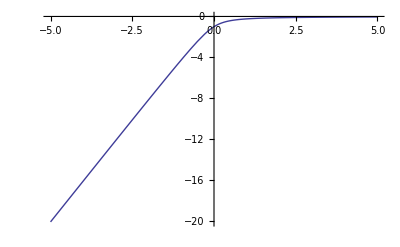

```mathematica
k=2;Plot[{f[k,x]},{x,-5,5}]
```

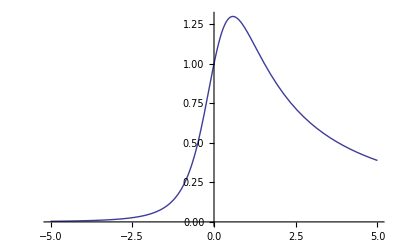

```mathematica
k=2;Plot[raf,{x,-5,5}]
```